```mathematica
SetDirectory[NotebookDirectory[]];
Get["../source/mathematica/AnalyticValence.wl"];
Get["../source/mathematica/FigureSettings.wl"];
InitializePlotSettings[]
```

```mathematica
{J,V,ϵ}={0.1,1,0.05};
II={0.6,0.8,1.0,1.2,1.4};
```

```mathematica
{ϕ1,p1,n1}=r2Results[J,II[[1]],V,ϵ];
{ϕ2,p2,n2}=r2Results[J,II[[2]],V,ϵ];
{ϕ3,p3,n3}=r2Results[J,II[[3]],V,ϵ];
{ϕ4,p4,n4}=r2Results[J,II[[4]],V,ϵ];
{ϕ5,p5,n5}=r2Results[J,II[[5]],V,ϵ];
```

```mathematica
pFuncs=(#[x]&)/@{p1,p2,p3,p4,p5};
nFuncs=(#[x]&)/@{n1,n2,n3,n4,n5};
phiFuncs=(#[x]&)/@{ϕ1,ϕ2,ϕ3,ϕ4,ϕ5};
```

```mathematica
pPlot=Plot[pFuncs,{x,0,1},PlotRange->{{0,1},{0.6,1.6}},PlotStyle->MapThread[Directive,{colors,dotting}],Frame->True,AspectRatio->1,ImageSize->400];
nPlot=Plot[nFuncs,{x,0,1},PlotRange->{{0,1},{0.6,1.6}},PlotStyle->MapThread[Directive,{colors,dotting}],Frame->True,AspectRatio->1,GridLines->Automatic,ImageSize->400];phiPlot=Plot[phiFuncs,{x,0,1},PlotRange-> {{0,1},{-0.2,1.2}},PlotStyle->MapThread[Directive,{colors,dotting}],Frame->True,AspectRatio->1,ImageSize->400];
```

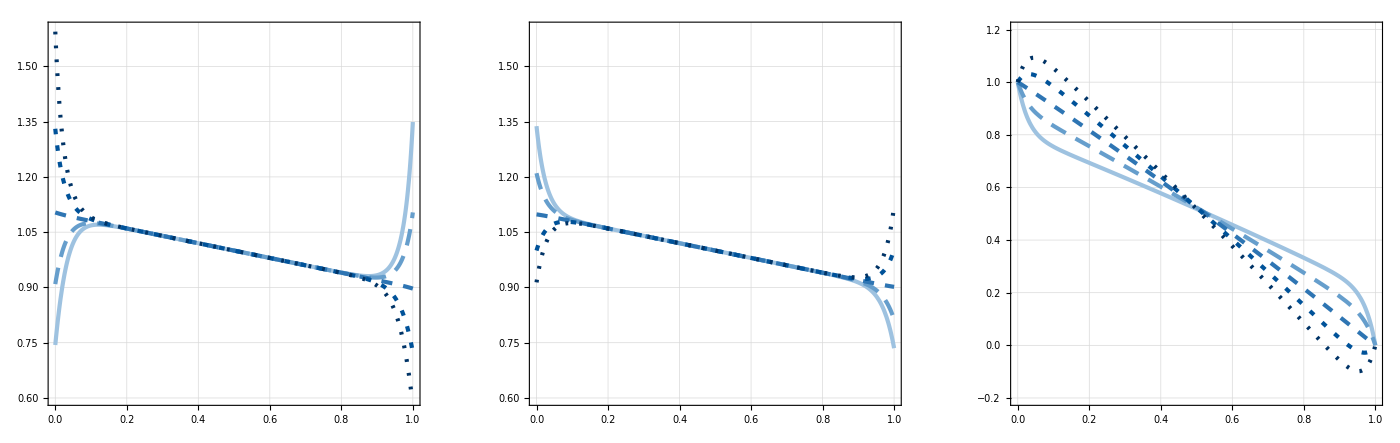

```mathematica
triptych=GraphicsRow[{pPlot,nPlot,phiPlot},Spacings->40,ImageSize->1400]
```

Labels and annotations added in photo editing software Canva.

```mathematica
Export[FileNameJoin[{NotebookDirectory[],"..","figures","Figure5.pdf"}],triptych,ImageResolution->300]
```

/Users/georginaryan/Desktop/DPhil/Research/Draft Papers/Journal Article - Chapter 4/Figures Ratio Version/Final Code for Repository/asymmetric-valence-electrolytes/notebooks/../figures/Figure5.pdf